-Graphics-

# Wolfram Language

## Principles and Concepts

-Graphics-

## Outline

### Structure

### Operation (Evaluation)

### Design

### Questions

## Structure

## Expressions

Everything in Wolfram Language (WL) is an expression—input and output

Examples:

```mathematica
3.1415926
```

```mathematica
3-2ⅈ
```

```mathematica
Head[%]
```

```mathematica
"Alice was beginning to get very tired of sitting by her sister on the bank, and of having nothing to do."
```

```mathematica
{1,1,2,3,5,8,13}
```

```mathematica
(-b+√(b^2-4a c))/(2a)
```

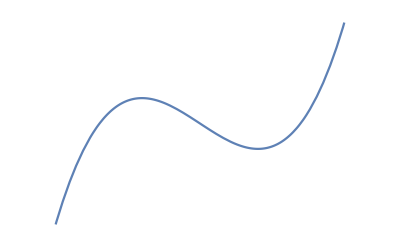

```mathematica
Quantity[75.43,"kilograms"]
```

```mathematica
Entity["Person","Charlemagne::9ffvv"]//FullForm
```

Because output is an expression, it can then be used directly as input

### Atomic expressions

Integer

Real

String

Symbol

Rational

```mathematica
1/2
```

```mathematica
Numerator[%]
```

Complex

```mathematica
3+5ⅈ
```

```mathematica
Im[%]
```

### Normal expressions

Head and body

```mathematica
f[x]
```

```mathematica
f[y,z,3]
```

Body may be empty

```mathematica
f[]
```

Head itself may be a normal expression

```mathematica
f[y][t]
```

### Compound atomic expressions

Graph

```mathematica
g=Graph[{a->b,b->c,b->d},VertexLabels->Automatic]
```

```mathematica
g[[2]]
```

```mathematica
AtomQ[g]
```

```mathematica
VertexList[g]
```

SparseArray

```mathematica
s=SparseArray[{{1,1}->1,{2,2}->2,{3,3}->3,{1,3}->4}]
```

```mathematica
MatrixForm[s]
```

```mathematica
s[[2]]
```

```mathematica
Normal@%
```

Association

```mathematica
kv=<|a->x,b->y,c->z|>
```

```mathematica
Keys[kv]
```

```mathematica
Values[kv]
```

```mathematica
kv[b]
```

```mathematica
kv[[2]]
```

```mathematica
Normal[kv]
```

```mathematica
KeyTake[kv,b]
```

Dataset

```mathematica
dataset=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{3}|>,
<|"a"->4,"b"->"x","c"->{4,5}|>,
<|"a"->5,"b"->"y","c"->{5,6,7}|>,
<|"a"->6,"b"->"z","c"->{}|>}]
```

```mathematica
dataset[1;;3]
```

```mathematica
dataset[3,"c"]
```

```mathematica
Head[%]
```

### Notation style

FullForm

```mathematica
Plus[2,Times[3,x]]
```

```mathematica
%//FullForm
```

```mathematica
Map[Abs,{-3,-2,-1,-0,1,2,3}]
```

Prefix

```mathematica
Column@{1,2,3}
```

Infix

```mathematica
2+x*x
```

```mathematica
Abs/@{-3,-2,-1,-0,1,2,3}
```

```mathematica
q=3;
r=4;
s=2;
q^(r-s)
```

Postfix

```mathematica
Map[Cos,{1,2,3}]//Mod[#,3]&
```

```mathematica
x=RandomInteger[{0,10},{5,3}]//Grid
```

```mathematica
Head[x]
```

```mathematica
(x=RandomInteger[{0,10},{5,3}])//Grid
```

```mathematica
x
```

```mathematica
x=RandomInteger[{0,10},{5,3}]//Echo[#,"x=",Grid]&
```

### Wrappers vs. modification

```mathematica
Eigenvalues[{{1,2,3},{4,5,6},{7,8,9}}]
```

```mathematica
N@%
```

```mathematica
NumberForm[%,2]
```

```mathematica
First[%]
```

```mathematica
Style["The big red barn.",Red,18]
```

```mathematica
FullForm[%]
```

```mathematica
Graphics[{Blue,Line[{{1,0},{0,2},{3,3}}]},ImageSize->Small]
```

```mathematica
FullForm[%]
```

## Mathematica Kernel & FrontEnd

### Your data’s round trip

On the desktop & Cloud you interact directly with the FrontEnd through your notebook document

When you press Shift-Enter, the FrontEnd parses your input into a FullForm expression and passes it to the Kernel

The Kernel evaluates the expression and returns the result to the FrontEnd as a FullForm expression

The FrontEnd renders the result in an appropriate manner in your notebook

### Documents

The notebook document is a Notebook expression in the memory of the FrontEnd

It’s written to the storage device as an expression

It can be, and sometimes is, read as data!

take a peek with TextEdit or Notepad

There are special comments included that allow the FrontEnd to handle the file efficiently

therefore, it’s best to edit the file only with the FrontEnd

## Symbols and character sets

WL has a rich set of characters, all of which can be used in strings and symbols

5 sets of letter characters

Latin (ASCII)

```mathematica
b=15
```

Script

```mathematica
𝒷=14
```

```mathematica
b
```

```mathematica
𝒷
```

Greek

Gothic

DoubleStruck

Nearly every symbol imaginable!

Enter as

FullForm

```mathematica
\[Beta] \[CapitalGamma]
```

Keyboard shortcut

EscbEsc EscGEsc

Pick from a pallet

## Mathematical notation & two-dimensional forms

### Typical computable input

Symbols can be augmented with traditional mathematical or scientific notations

```mathematica
x=.
```

```mathematica
Clear[x]
```

```mathematica
1/(2+x)
```

```mathematica
FullForm[%]
```

Most are only wrappers, a few have special interpretation in WL

Superscript ⟶ Power

```mathematica
3^2
```

```mathematica
3^2
```

```mathematica
Superscript[3,2]
```

```mathematica
FullForm[%]
```

```mathematica
x^2
```

```mathematica
FullForm[%]
```

Superscript Prime ⟶ Derivative

```mathematica
x'[t]==-x
```

```mathematica
FullForm[%]
```

One can define special interpretation rules

```mathematica
<<Chemistry`ChemicalKinetics`
```

```mathematica
Reaction[A+B,Subscript[k, f],C,Subscript[k, r]]
```

```mathematica
Subscript[k, f]
```

```mathematica
FullForm[%]
```

### Cautionary note

```mathematica
DSolve[{x'[t]==x[t]-Subscript[a, max],x[0]==Subscript[x, 0]},x[t],t]
```

```mathematica
DSolve[{x'[t]==x[t]-Subscript[a, max],x[0]==x0},x[t],t]
```

## Operation (Evaluation)

## Parsing into FullForm

The usual rules of algebra apply:

exponentiation > {multiplication
division > {addition
subtraction > negation

All operators (e.g., ⊗) have a precedence assigned to them

Use parentheses for explicit grouping, not curly braces (List) or brackets (normal expression syntax)

## A sidebar

Wrapping Hold around an expression will prevent it from evaluating

```mathematica
Hold[2+3]
```

```mathematica
FullForm[%]
```

ReleaseHold does just that

```mathematica
ReleaseHold[%]
```

Useful for building up an expression before evaluating it, or programmatically constructing a function from data

Also useful in examples in a presentation

## Steps in the evaluation process

Full details at the tutorial Evaluation

Overview:

If the expression is a raw object (atomic, Integer, String, etc.), leave it unchanged

Evaluate the head of the expression

Evaluate each element of the expression, left to right

Use any applicable user-defined transformation rules associated with the head of the expression

Use any built-in transformation rules associated with the head of the expression

Note that the phrase apply transformation rule is used, and not arguments are passed

The “lines of code” in a function appear to be terminated by semicolons (;)

; is the infix form for CompoundExpression

```mathematica
Hold[
Module[{a},
a=5;
a=a^2;
a-2]
]//FullForm
```

## Step-By-Step—Trace

Trace exposes each step of an evaluation

```mathematica
x=1;
y[i_]:=i+2;
```

```mathematica
Trace[x^2+y[x]-4]
```

```mathematica
Column[%]
```

TracePrint exposes selected steps of an evaluation

```mathematica
TracePrint[x^2+y[x]-4,_y]
```

## Head vs arguments

The head of an expression is always evaluated first

Depending on the Attributes of the head, all or only some of the arguments are evaluated

More about Attributes in a later lecture

## Design

## Wolfram Language

Similar functions take similarly structured input and produce similarly structured output

Options always come at the end of the list of arguments

```mathematica
Style["the quick brown fox",FontSize->72]
```

WL supports different coding styles:

procedural

functional

rule-based

WL tries to automate as much as possible in high-level functions

Provide for fine control via options with reasonable default values

```mathematica
?ClusteringTree
```

```mathematica
FilterRules[Options[ClusteringTree],Except[Options[Graph]]]//Column
```

## Your code

Use the coding style with which you are most comfortable

Use the coding style that most clearly and most generally defines the operation on the data

You, or someone else, will want to know what the code does at some point in the future

You may need to adapt or extend the code to handle new instances of the data

Try to follow existing precedents

Same option names for the same purpose

If your function takes and iteration count, then overload it to accept max, {min,max}, {min,max,incr}

Modularity

One “operation” per function

keeps code manageable: building blocks

generally makes debugging easier

Allows code reuse

## Questions